```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},EdgeCount[g]==6+2&&EdgeQ[g,2<->3]&&EdgeQ[g,2<->4]&&EdgeQ[g,2<->5]&&EdgeQ[g,3<->4]&&EdgeQ[g,3<->5]&&EdgeQ[g,4<->5]&&EdgeQ[g,2<->1]&&EdgeQ[g,5<->1]]&]
```

{20776}

```mathematica
allGraphs5[K4Key,"graph"]//EdgeList
```

{2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
allGraphs5[20776,"graph"]
```

-Graphics-

```mathematica
MobiusGraph5[20776,allGraphs5]//VertexList
```

{n123x4x5,n124x3x5,n12x34x5,n12x35x4,n12x3x45,n135x2x4,n145x2x3,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n135x24,n145x23,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
ListofVars[allGraphs5[20776,"colofourrealnull"]]
```

{n123x4x5,n124x3x5,n12x34x5,n12x35x4,n12x3x45,n135x2x4,n145x2x3,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n135x24,n145x23,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[prefix<> StringDrop[SymbolName[s],1]]
```

```mathematica
Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[20776,"colofour"]]]
```

{n13x2x4x5,n14x2x3x5,n1x2x3x4x5}

```mathematica
{n13x2x4x5,n14x2x3x5,n1x2x3x4x5}{n13x2x4x5,n14x2x3x5,n1x2x3x4x5}
```

{0,0,0}

```mathematica
Mob5ForKey[key_]:=With[
{goodVertices=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[key,"colofour"]]],
baseGraph=MobiusGraph5[K5Key,allGraphs5],
formula=allGraphs5[key,"colofour"]},
Labeled[Rotate[Graph[baseGraph,VertexStyle->Table[v->If[MemberQ[goodVertices,v],Green,Red],{v,VertexList[baseGraph]}],GraphHighlightStyle->"DehighlightFade",ImageSize->800],Pi/2],
{ShowGraph[allGraphs5,key],Map[Last,Sort[Tally[Map[StringCount[SymbolName[#],"x"]-1&,ListofVars[formula]]]]]}
]
]
```

```mathematica
MobForKey[allGraphs_,key_]:=With[{
kx=FromDigits[Table[1,{k,TriangleNumber[VertexCount[allGraphs[0,"graph"]]-1]}],3]
},
With[
{goodVertices=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs[key,"colofour"]]],
baseGraph=MobiusGraph5[kx,allGraphs],
formula=allGraphs[key,"colofour"]},
Labeled[Rotate[Graph[baseGraph,VertexStyle->Table[v->If[MemberQ[goodVertices,v],Green,Red],{v,VertexList[baseGraph]}],GraphHighlightStyle->"DehighlightFade",ImageSize->800],Pi/2],
{ShowGraph[allGraphs,key],Map[Last,Sort[Tally[Map[StringCount[SymbolName[#],"x"]-1&,ListofVars[formula]]]]]}
]
]
]
```

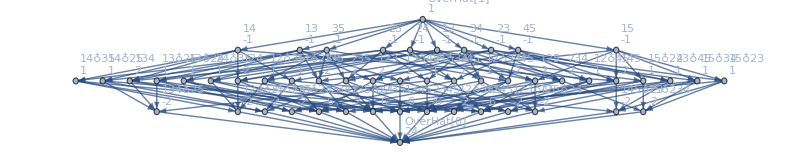
-Graphics-{-Graphics-364,{4,1}}

```mathematica
MobForKey[allGraphs5,K4Key]
```

```mathematica
Mob5ForKey[20776]
```

-Graphics-{-Graphics-20776,{2,1}}

```mathematica
Mob5ForKey[K4Key]
```

-Graphics-{-Graphics-364,{4,1}}

```mathematica
Mob5ForKey[K3Key]
```

-Graphics-{-Graphics-13,{9,7,1}}

```mathematica
IntegerDigits[K3Key,3]
```

{1,1,1}

```mathematica
Mob5ForKey[1]
```

-Graphics-{-Graphics-1,{8,19,9,1}}

```mathematica
CountSols[key_,all_]:=Block[{formula=all[key,"colofour"]},
Map[Last,Sort[Tally[Map[StringCount[SymbolName[#],"x"]-1&,ListofVars[formula]]]]]
]
```

```mathematica
Table[CountSols[1,all],{all,{allGraphs2, allGraphs3,allGraphs4,allGraphs5,allGraphs6}}]//TableForm
```

1 |  |  |  | 
2 | 1 |  |  | 
4 | 5 | 1 |  | 
8 | 19 | 9 | 1 | 
16 | 65 | 55 | 14 | 1

```mathematica
Table[CountSols[K3Key,all],{all,{allGraphs3,allGraphs4,allGraphs5,allGraphs6}}]//TableForm
```

1 |  |  | 
3 | 1 |  | 
9 | 7 | 1 | 
27 | 37 | 12 | 1

```mathematica
Table[CountSols[K4Key,all],{all,{allGraphs4,allGraphs5,allGraphs6}}]//TableForm
```

1 |  | 
4 | 1 | 
16 | 9 | 1

```mathematica
rep5=Table[allGraphs5[k,"colofour"]-> ShowGraph[allGraphs5,k],{k,allGraphs5AtomKeys}];
```

```mathematica
rep5Null=Table[allGraphs5[k,"colofourrealnull"]-> ShowGraph[allGraphs5,k],{k,allGraphs5NullAtomKeys}];
```

```mathematica
allGraphs5[K4Key,"colofour"]/.rep5
```

-Graphics-49207+-Graphics-36085+-Graphics-31711+-Graphics-30253+-Graphics-29524

```mathematica
allGraphs5[K4Key,"colofourrealnull"]/.rep5Null
```

-6 -Graphics-728+2 -Graphics-666+2 -Graphics-546+-Graphics-488+2 -Graphics-218+-Graphics-72+2 -Graphics-26+-Graphics-168--Graphics-486--Graphics-162--Graphics-18--Graphics-54--Graphics-2--Graphics-6+-Graphics-0

```mathematica
GraphSpectrum[g_]:=Block[{form=FindFullFormula[g],
n=VertexCount[g],
counts},
counts=Table[StringCount[SymbolName[s],"x"]+1,{s,ListofVars[form]}];
Table[Length[Select[counts,#==k&]],{k,1,n}]
]
```

```mathematica
Table[GraphSpectrum[all[1,"graph"]],{all,{allGraphs2, allGraphs3,allGraphs4,allGraphs5,allGraphs6}}]//TableForm
```

0 | 1 |  |  |  | 
0 | 2 | 1 |  |  | 
0 | 4 | 5 | 1 |  | 
0 | 8 | 19 | 9 | 1 | 
0 | 16 | 65 | 55 | 14 | 1

```mathematica
Table[StirlingS2[n,k]-StirlingS2[n-1,k],{n,2,20},{k,1,20}]//TableForm
```

0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 19 | 9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16 | 65 | 55 | 14 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32 | 211 | 285 | 125 | 20 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 64 | 665 | 1351 | 910 | 245 | 27 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 128 | 2059 | 6069 | 5901 | 2380 | 434 | 35 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 256 | 6305 | 26335 | 35574 | 20181 | 5418 | 714 | 44 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 512 | 19171 | 111645 | 204205 | 156660 | 58107 | 11130 | 1110 | 54 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1024 | 58025 | 465751 | 1132670 | 1144165 | 563409 | 147147 | 21120 | 1650 | 65 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2048 | 175099 | 1921029 | 6129101 | 7997660 | 5088028 | 1740585 | 337227 | 37620 | 2365 | 77 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4096 | 527345 | 7859215 | 32566534 | 54115061 | 43613856 | 19012708 | 4775628 | 713427 | 63635 | 3289 | 90 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8192 | 1586131 | 31964205 | 170691885 | 357256900 | 359412053 | 195715520 | 61993360 | 11909898 | 1413412 | 103103 | 4459 | 104 | 1 | 0 | 0 | 0 | 0 | 0
0 | 16384 | 4766585 | 129442951 | 885423630 | 2314233285 | 2873141271 | 1925136213 | 753655760 | 181092340 | 27457430 | 2650648 | 161070 | 5915 | 119 | 1 | 0 | 0 | 0 | 0
0 | 32768 | 14316139 | 522538389 | 4556561101 | 14770823340 | 22426222182 | 18274230975 | 8708038053 | 2564579160 | 483124070 | 59265206 | 4744558 | 243880 | 7700 | 135 | 1 | 0 | 0 | 0
0 | 65536 | 42981185 | 2104469695 | 23305343894 | 93181501141 | 171754378614 | 168620069982 | 96646573452 | 34353829653 | 7878943930 | 1194306542 | 120944460 | 8158878 | 359380 | 9860 | 152 | 1 | 0 | 0
0 | 131072 | 129009091 | 8460859965 | 118631189165 | 582394350740 | 1295462151439 | 1520714938470 | 1038439231050 | 440184869982 | 121022212883 | 22210622434 | 2766584522 | 235168752 | 13549578 | 517140 | 12444 | 170 | 1 | 0
0 | 262144 | 387158345 | 33972448951 | 601616805790 | 3612997293605 | 9650629410813 | 13461181659199 | 10866668017920 | 5440287930870 | 1771429211695 | 387549682091 | 58176221220 | 6058947050 | 438412422 | 21823818 | 728688 | 15504 | 189 | 1

```mathematica
Table[StirlingS2[n,k]-6StirlingS2[n-1,k]+11StirlingS2[n-2,k]-6StirlingS2[n-3,k],{n,4,20},{k,2,20}]//TableForm
```

0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16 | 9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 64 | 61 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 256 | 369 | 151 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1024 | 2101 | 1275 | 305 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4096 | 11529 | 9751 | 3410 | 545 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16384 | 61741 | 70035 | 33621 | 7770 | 896 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 65536 | 325089 | 481951 | 305382 | 95781 | 15834 | 1386 | 60 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 262144 | 1690981 | 3216795 | 2619625 | 1071630 | 238287 | 29694 | 2046 | 72 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1048576 | 8717049 | 20991751 | 21554170 | 11192665 | 3216213 | 535227 | 52200 | 2910 | 85 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4194304 | 44633821 | 134667555 | 171870941 | 111095490 | 40138582 | 8568483 | 1109427 | 87120 | 4015 | 99 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16777216 | 227363409 | 852639151 | 1337764142 | 1060634861 | 472342728 | 125823412 | 20772180 | 2154867 | 139315 | 5401 | 114 | 1 | 0 | 0 | 0 | 0
0 | 0 | 67108864 | 1153594261 | 5343198315 | 10216988145 | 9822843030 | 5311719413 | 1730576848 | 354317392 | 46630584 | 3965962 | 214929 | 7111 | 130 | 1 | 0 | 0 | 0
0 | 0 | 268435456 | 5835080169 | 33212784151 | 76862115330 | 88799732385 | 57628317747 | 22617487893 | 5628068160 | 913884400 | 98188090 | 6974968 | 321594 | 9191 | 147 | 1 | 0 | 0
0 | 0 | 1073741824 | 29443836301 | 205111785075 | 571247591461 | 787259974410 | 607454592108 | 283803196677 | 84526237653 | 16594680960 | 2190329570 | 195837642 | 11798878 | 468650 | 11690 | 165 | 1 | 0
0 | 0 | 4294967296 | 148292923329 | 1260114546751 | 4203844925302 | 6869327386741 | 6254351303382 | 3445486558878 | 1213591810860 | 283662409173 | 45068965370 | 4932056558 | 372820812 | 19297278 | 667380 | 14660 | 184 | 1

```mathematica
Sum[StirlingS2[n-x,k]*StirlingS1[4,4-x],{x,0,3}]
```

-6 StirlingS2[-3+n,k]+11 StirlingS2[-2+n,k]-6 StirlingS2[-1+n,k]+StirlingS2[n,k]

```mathematica
Table[StirlingS1[4,4-x],{x,0,3}]
```

{1,-6,11,-6}

```mathematica
Table[Sum[StirlingS2[n-x,k]*StirlingS1[4,4-x],{x,0,3}],{n,4,20},{k,2,20}]//TableForm
```

0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16 | 9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 64 | 61 | 15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 256 | 369 | 151 | 22 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1024 | 2101 | 1275 | 305 | 30 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4096 | 11529 | 9751 | 3410 | 545 | 39 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16384 | 61741 | 70035 | 33621 | 7770 | 896 | 49 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 65536 | 325089 | 481951 | 305382 | 95781 | 15834 | 1386 | 60 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 262144 | 1690981 | 3216795 | 2619625 | 1071630 | 238287 | 29694 | 2046 | 72 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1048576 | 8717049 | 20991751 | 21554170 | 11192665 | 3216213 | 535227 | 52200 | 2910 | 85 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4194304 | 44633821 | 134667555 | 171870941 | 111095490 | 40138582 | 8568483 | 1109427 | 87120 | 4015 | 99 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16777216 | 227363409 | 852639151 | 1337764142 | 1060634861 | 472342728 | 125823412 | 20772180 | 2154867 | 139315 | 5401 | 114 | 1 | 0 | 0 | 0 | 0
0 | 0 | 67108864 | 1153594261 | 5343198315 | 10216988145 | 9822843030 | 5311719413 | 1730576848 | 354317392 | 46630584 | 3965962 | 214929 | 7111 | 130 | 1 | 0 | 0 | 0
0 | 0 | 268435456 | 5835080169 | 33212784151 | 76862115330 | 88799732385 | 57628317747 | 22617487893 | 5628068160 | 913884400 | 98188090 | 6974968 | 321594 | 9191 | 147 | 1 | 0 | 0
0 | 0 | 1073741824 | 29443836301 | 205111785075 | 571247591461 | 787259974410 | 607454592108 | 283803196677 | 84526237653 | 16594680960 | 2190329570 | 195837642 | 11798878 | 468650 | 11690 | 165 | 1 | 0
0 | 0 | 4294967296 | 148292923329 | 1260114546751 | 4203844925302 | 6869327386741 | 6254351303382 | 3445486558878 | 1213591810860 | 283662409173 | 45068965370 | 4932056558 | 372820812 | 19297278 | 667380 | 14660 | 184 | 1

```mathematica
Table[Sum[StirlingS2[n-x,k]*StirlingS1[5,5-x],{x,0,5-1}],{n,5,20},{k,2,20}]//TableForm
```

0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 25 | 11 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 125 | 91 | 18 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 625 | 671 | 217 | 26 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3125 | 4651 | 2190 | 425 | 35 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 15625 | 31031 | 19981 | 5590 | 740 | 45 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 78125 | 201811 | 170898 | 64701 | 12250 | 1190 | 56 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 390625 | 1288991 | 1398097 | 688506 | 174951 | 24150 | 1806 | 68 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1953125 | 8124571 | 11075670 | 6906145 | 2263065 | 416451 | 44016 | 2622 | 81 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 9765625 | 50700551 | 85654261 | 66324830 | 27273730 | 6427575 | 900627 | 75480 | 3675 | 95 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 48828125 | 313968931 | 650280378 | 616252901 | 311788400 | 91549480 | 16334472 | 1806387 | 123255 | 5005 | 110 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 244140625 | 1932641711 | 4865931577 | 5580303586 | 3422348501 | 1227283200 | 271228672 | 38011116 | 3408702 | 193325 | 6655 | 126 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1220703125 | 11839990891 | 35994162750 | 49508360265 | 36381440095 | 15695180501 | 4210798592 | 727362064 | 82324242 | 6115252 | 293150 | 8671 | 143 | 1 | 0 | 0
0 | 0 | 0 | 6103515625 | 72260648471 | 263799130141 | 432061044870 | 376941321120 | 193333245105 | 62013965013 | 12939143360 | 1797577210 | 167937770 | 10512502 | 431886 | 11102 | 161 | 1 | 0
0 | 0 | 0 | 30517578125 | 439667406451 | 1918854559458 | 3720287489101 | 3824532934950 | 2310273772170 | 875486860248 | 217283685333 | 36307647090 | 4148705990 | 325625300 | 17422678 | 620620 | 14000 | 180 | 1

```mathematica
Stirling2(n,k)-6*Stirling2(n-1,k)+11*Stirling2(n-2,k)-6*Stirling2(n-3,k)
```